# Mathematica Research Project - ALCOHOL CONSUMPTION IMPACT ON ACADEMIC GRADE PREDICTOR

## Introduction

## Aim of this research project:

Alcohol misuse is one of the most serious public health problems facing adolescents and young adults. National statistics shows that alcohol consumed by youth under 21 years of age engage in high-risk drinking activities nonfatal or fatal injuries, alcohol poisoning, blackouts, academic failure, violence (which includes rape and assault), and sexually transmitted diseases, to criminal activities that may jeopardize future life prospects. In this project, I have chosen to find impact of alcohol consumption on the academic grade. The aim is to study whether students consuming more alcohol are more likely to underperform and get lower grades.

## Underlying features:

In the following Mathematica file I will explore various possibilities of working with a dataset in Mathematica, including descriptive and exploratory statistics, visualisation, regression and prediction.
     * In order to carry out the Data Pre-processing part successfully, several steps have been taken including data cleaning, checking data distribution, correlation, interdependence of variables   (multicollinearity), outlier detection etc.
     * The Analysis part will consist of model fitting, computing several model parameters like AIC, Confidence Interval, P-values etc., grade prediction, study of alcohol consumption on daily vs on weekend.
     * The Visualization part helps to view 2D and 3D plots of the results obtained during analysis.

## Descriptive and Exploratory Statistics

#### Basics

In order to carry out some exploratory statistics, I will use a mixture of plotting and other functions, listed here:

Histogram                                plots a histogram with bin width specification.

Box Plot                                    BoxWhiskerChart gives a box plot indicating 1st Quartile, 3rd Quartile, Minimum, Maximum, Median and Unusually extreme entries(probable outliers).

ListPlot                                      plots a list of points with specified x and y coordinates.

ListPlot3D                                 plots a list of points with specified x, y and z coordinates.

Plot                                    	    plots function of 1 variable.

Manipulate                               plots interactive parameters in a function. It allows us to generate a plot with sliders to change the value of certain parameters.

The  dataset used in this project  is taken from www.kaggle.com, which includes age, sex, grade, and several other variables, listed below :

sex                                                - gender of student (Male / Female)

age                                               - age of student (varies between 15-22)

travel_time                               - time invested in travel between home to school

study_time                                - time invested daily for study purpose

failures                                        - total number of past failures of the student

daily                                             - total number of unit alcohol consumption on daily basis

weekend                                     - total number of unit alcohol consumption on weekend

absence                                      - total number of past absences from school

Grade                                         - Grade of a student -> This is the target variable!

For the data analytics project in Mathematica, I have used Mathematica For Prediction Utilities, which enables to readily use features like summary statistics, plots etc.

Importing required packages

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MosaicPlot.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/R/DataConversionFunctions.R"];
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MonadicProgramming/MonadicEventRecordsTransformations.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MonadicProgramming/MonadicTracing.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/WeatherEventRecords.m"]
```

In order to read in the dataset successfully and to further be able to use the “Dataset” functionality of Mathematica, which represents a structured dataset based on a hierarchy of lists and associations, following code is applied:

Import of Training Set

```mathematica
(*Setting working directory, reading from CSV file and converting to table format for better view*)
SetDirectory[$UserDocumentsDirectory];
studentData = Import["student.csv"];
stdata=Import["student.csv","Data"];
TableForm[Take[Rest@stdata,33], TableHeadings->{None,First@stdata}];
```

After loading data, converting it to the form required for analysis. Storing labels, separating columns from headings and storing in the form of table.

```mathematica
labels = First@stdata  (*first row set as table heading labels*)
columns = labels //ToExpression;
data = Rest@stdata ;    (*data variable contains all data except header row*)
Table[Set[Evaluate[columns[[i]]],i],{i, Length[columns]}];
```

{sex,age,traveltime,studytime,failures,Dalc,Walc,absences,Grade}

Need to split data into training set and test set. I have split the data into 80:20 ratio.
Training set is used to train the model whereas, test set is used to test the model.

```mathematica
SeedRandom[100];
n = Length[data];(*n storing length of data*)
testDataId = RandomSample[Range[n], Round[.2n]]; (*splitting data into training and testing dataset. 20% to test the model*)
testData = data[[testDataId]];
trainData = data[[Complement[Range[n], testDataId]]]; (*80% of the total data to train the model*)
```

storing all variables individually for quick modification and flexible usage

```mathematica
SEX = trainData[[2;;,1]];
age=trainData[[2;;,2]];
travel=trainData[[2;;,3]];
study=trainData[[2;;,4]];
failure=trainData[[2;;,5]];
daily=trainData[[2;;,6]];
weekly=trainData[[2;;,7]];
absence=trainData[[2;;,8]];
grade=trainData[[2;;,9]];
```

Storing transpose of the data except target variable. Storing target variable separately.

```mathematica
numdata={grade, SEX,age,travel,study, failure, daily,weekly,absence};
numdataT = Transpose[numdata];
numpredict = {SEX,age,travel,study, failure, daily,weekly,absence}//Transpose;
numresponse = grade;
```

Viewing summary of variables to analyse Minimum, Maximum, 1st Quartile, 3rd Quartile, Mean, Median.

```mathematica
RecordsSummary[trainData, labels]   (*Summary of all categorical and numeric columns*)
```

{1 sex
1st Qu | 0
Min | 0
Mean | 0.585742
3rd Qu | 1
Max | 1
Median | 1,2 age
Min | 15
1st Qu | 16
Mean | 16.7264
Median | 17
3rd Qu | 18
Max | 22,3 traveltime
1st Qu | 1
Median | 1
Min | 1
Mean | 1.54913
3rd Qu | 2
Max | 4,4 studytime
1st Qu | 1
Min | 1
Mean | 1.94798
3rd Qu | 2
Median | 2
Max | 4,5 failures
1st Qu | 0
3rd Qu | 0
Median | 0
Min | 0
Mean | 0.22736
Max | 3,6 Dalc
1st Qu | 1
Median | 1
Min | 1
Mean | 1.50289
3rd Qu | 2
Max | 5,7 Walc
1st Qu | 1
Min | 1
Median | 2
Mean | 2.26975
3rd Qu | 3
Max | 5,8 absences
1st Qu | 0
Min | 0
Median | 2
Mean | 3.59345
3rd Qu | 6
Max | 30,9 Grade
Min | 5
1st Qu | 10
Median | 11
Mean | 11.4721
3rd Qu | 13
Max | 19}

There is no missing data in the input file to be handled. The data is free from NA values. and hence can be used as it is.

```mathematica
(*Get["./MathematicaForPrediction/MosaicPlot.m"];*)
```

Importing from GitHub: MosaicPlot.m

Importing from GitHub: CrossTabulate.m

This variable dependence grid shows the relationships between the variables.

```mathematica
Magnify[#,0.7]&@VariableDependenceGrid[trainData,labels]
```

-Graphics-

Importing from GitHub: DataReshape.m

Checking Histograms for the distribution of variables. After analysing the histogram, it is very clear that the target variable “Grade” is normally distributed. Number of Male students are more than Female students. Rest of the variables are showing right skewness implying that the mean is on the right side of the median.

```mathematica
Histogram[SEX, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Sex"]
Histogram[age, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Age"]
Histogram[travel, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Travel Time"]
Histogram[study, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Study Time"]
Histogram[failure, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of No. of Failures"]
Histogram[daily, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Daily Alcohol Consumption"]
Histogram[weekly, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Alcohol Consumption on Weekend"]
Histogram[absence, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Absence from school"]
Histogram[grade, PlotTheme->"Marketing", ColorFunction->"Rainbow", PlotLabel->"Histogram of Grade"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Bar Chart Plot (BoxWhiskerChart) helps us to have a top view of the data distribution of the predictor and response variables. It is showing minimum, maximum, median, 1st and 3rd quartile. Also, the possible outliers in the data corresponding to unusually high or low values. Absences from school shows a lot of probable outliers. Other variables have lesser number of outliers.

```mathematica
(*Plotting boxcharts to study behaviour of variables in form of box, studying median, 1st quartile, 3rd quartile, minima and maxima*)
BoxWhiskerChart[{age,travel, study, failure, daily, weekly, absence, grade}, "Outliers", PlotTheme->"Marketing", ChartLabels->{"Age","Travel Time","StudyTime","No. of Failures", "Daily Alcohol Consumption","Weekly Alcohol COnsumption","No. of Absences from school","Grade"}, ImageSize->Full]
```

-Graphics-

Fitting model using LinearModelFit.
Parameter Table gives Estimated values, Standard Error. P-Values which are extremely low are highly significant in the model like age, study, failure, daily,absence have very low p-values.

```mathematica
model1 = LinearModelFit[numdataT,{s,a,t,st,f,d,w,ab},{s,a,t,st,f,d,w,ab}]
mod1 = LinearModelFit[{numpredict, numresponse}];
Normal[mod1];
mod1["FitResiduals"];
mod1["BestFit"];
mod1["ParameterTable"]
{sr,fr}=mod1[{"StandardizedResiduals","FitResiduals"}];
{{ListPlot[sr, ImageSize->Medium, PlotLabel->"Standardized Residuals" ,Frame->True, Filling->Bottom],ListPlot[fr, PlotLabel->"Fit Residuals",Frame->True, Filling->Bottom]}}//GraphicsGrid
```

FittedModel[0.135075+0.571129 a+0.304625 ab+0.440367 d-0.342603 f-0.135737 s-0.127902 st+0.236078 t+0.538435 w]

| Estimate | Standard Error | t-Statistic | P-Value
#1 | 0.22999 | 0.236681 | 0.971729 | 0.331646
#2 | 0.652291 | 0.0283698 | 22.9924 | 8.40063×10^-81
#3 | -0.153989 | 0.145602 | -1.0576 | 0.290739
#4 | 0.758103 | 0.134695 | 5.6283 | 3.0072×10^-8
#5 | -1.92869 | 0.188808 | -10.2151 | 2.05865×10^-22
#6 | -0.356276 | 0.150884 | -2.36126 | 0.0185881
#7 | 0.120382 | 0.11123 | 1.08228 | 0.279641
#8 | -0.0434811 | 0.0250974 | -1.73249 | 0.08379

Following plots show Standardized and Fit Residuals for analysis. The difference between an observed value and the value predicted by the model, Standardized . The residual divided by an estimate of its standard deviation, Standardized residuals. I plotted residual plot against all variables and fitted vs residual to check if the residuals do not exhibit any significant pattern or not. All graphs are random and there is no significant pattern observed

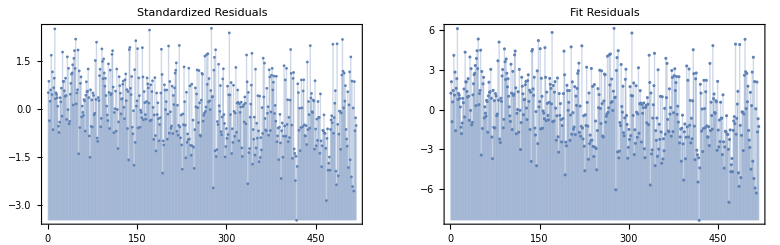

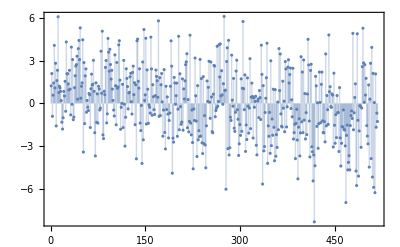

```mathematica
ListPlot[mod1["FitResiduals"], Frame->True, Filling->Axis]
```

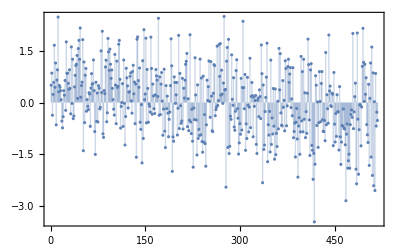

```mathematica
ListPlot[mod1["StandardizedResiduals"], Frame->True, Filling->Axis]
```

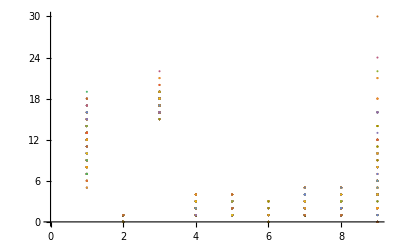

```mathematica
ListPlot[numdataT]
```

To find outliers, I computed cooks distance. It is observed that no point is actually influencing the model in the cooks plot. This was determined as there is no point have CookDistance >0.008.

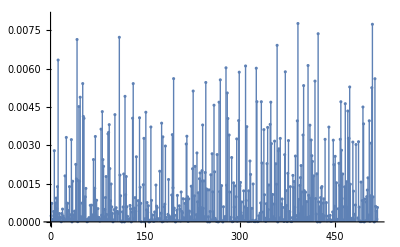

```mathematica
ListPlot[mod1["CookDistances"],Filling->0,FillingStyle-> None,PlotStyle->Thick]
```

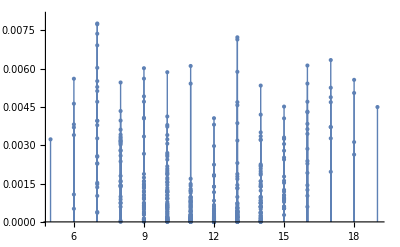

```mathematica
ListPlot[Transpose[{numdataT[[All,1]],mod1["CookDistances"]}],Filling->Axis,FillingStyle->Thick,PlotStyle->Thick]
```

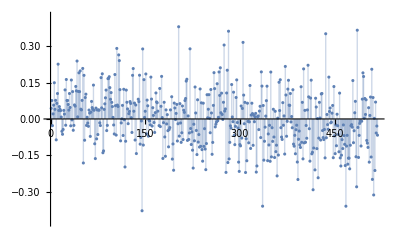

```mathematica
ListPlot[mod1["FitDifferences"],Filling->Axis]
```

```mathematica
mod1["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
mod1["BestFitParameters"]
```

{0.22999,0.652291,-0.153989,0.758103,-1.92869,-0.356276,0.120382,-0.0434811}

AIC stands for Akaike’s Information Criteria. The basic idea of AIC is to penalize the inclusion of additional variables to a model. It adds a penalty that increases the error when including additional terms. The lower the AIC, the better the model. AIC estimates the quality of each model, relative to each of the other models for the same dataset. It provides a means for model selection. The basic idea behind AIC is the model using less number of parameters is better.
AIC of mod1 is lower than that of model1, showing improvement in the fitted model.

```mathematica
model1["AIC"]
mod1["AIC"]
```

3003.39

2416.18

```mathematica
mod1["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
#1 | 1 | 41709.7 | 41709.7 | 6844.64 | 1.04887×10^-297
#2 | 1 | 25874. | 25874. | 4245.97 | 2.0268×10^-249
#3 | 1 | 24.4018 | 24.4018 | 4.00439 | 0.0459114
#4 | 1 | 404.258 | 404.258 | 66.3396 | 2.94098×10^-15
#5 | 1 | 676.709 | 676.709 | 111.049 | 1.26231×10^-23
#6 | 1 | 36.1409 | 36.1409 | 5.93079 | 0.0152202
#7 | 1 | 5.74151 | 5.74151 | 0.942194 | 0.332174
#8 | 1 | 18.2907 | 18.2907 | 3.00154 | 0.08379
Error | 510 | 3107.82 | 6.09377 |  | 
Total | 518 | 71857. |  |  |

R squared value can be misleading when we assess the goodness of fit of the linear regression model. 
The addition of predictors increases the R squared value and appears to be a better fit. However, a model with too many predictors and higher order polynomials begins to train the random noise in the data, leading to over-fitting of the model. To address this, Adjusted R square is used which adjusts the R2 for having too many variables in the model. The adjusted R-squared increases only if the new term improves the model more than would be expected by chance and decreases when a predictor improves the model by less than expected by chance. 
Adjusted R squared is always lower than the R-squared.
R2 value of the mod1 is 95.675% and Adjusted R2 is 95.6071%

As can be seen below in 2 models, model performance has been significantly improved from model1 to mod1 as the value of both R2 and Adjusted R2 has increased from 73.3% to 95.6% and 58.7 to 95.6 respectively.

```mathematica
model1["RSquared"]
mod1["RSquared"]
```

0.0733042

0.95675

```mathematica
model1["AdjustedRSquared"]
mod1["AdjustedRSquared"]
```

0.0587393

0.956071

```mathematica
mod1["ParameterTStatistics"]
```

{0.971729,22.9924,-1.0576,5.6283,-10.2151,-2.36126,1.08228,-1.73249}

```mathematica
mod1["BIC"]
```

2454.43

Correlation matrix explains if the variables have positive or negative relationships. Also, it tells about the strength of the relationship whether its strong, moderate or weak. 
• 	If the absolute value is above 60% it is considered as strong.
•	If the absolute value is above 40% and below 60%, it is considered as moderate.
•	If the absolute value is above 40% and below 60%, it is considered as moderate.
Following table shows no value greater than, implies that there is no multi-co linearity amongst the predictor variables. Otherwise, there would have been need to add interaction terms to the model.

```mathematica
mod1["CorrelationMatrix"]//MatrixForm
```

(1. | -0.370835 | 0.0356281 | -0.13472 | 0.0379551 | 0.0892132 | 0.191571 | -0.0576649
-0.370835 | 1. | -0.436741 | -0.599929 | -0.155189 | -0.15307 | -0.355564 | -0.138087
0.0356281 | -0.436741 | 1. | -0.0115196 | -0.0674622 | -0.0457509 | -0.0300447 | 0.0182182
-0.13472 | -0.599929 | -0.0115196 | 1. | 0.178851 | -0.00527437 | 0.121584 | 0.0831579
0.0379551 | -0.155189 | -0.0674622 | 0.178851 | 1. | -0.0317062 | 0.0272022 | -0.0931873
0.0892132 | -0.15307 | -0.0457509 | -0.00527437 | -0.0317062 | 1. | -0.573883 | -0.0980804
0.191571 | -0.355564 | -0.0300447 | 0.121584 | 0.0272022 | -0.573883 | 1. | -0.0656291
-0.0576649 | -0.138087 | 0.0182182 | 0.0831579 | -0.0931873 | -0.0980804 | -0.0656291 | 1.)

```mathematica
mod1["CovarianceMatrix"]//MatrixForm
```

(0.0560181 | -0.00249001 | 0.00122779 | -0.00429484 | 0.00169611 | 0.00318593 | 0.00504333 | -0.000342535
-0.00249001 | 0.000804846 | -0.00180405 | -0.00229249 | -0.000831262 | -0.000655225 | -0.00112201 | -0.0000983187
0.00122779 | -0.00180405 | 0.0212 | -0.000225921 | -0.00185459 | -0.0010051 | -0.000486586 | 0.0000665736
-0.00429484 | -0.00229249 | -0.000225921 | 0.0181427 | 0.00454845 | -0.000107193 | 0.00182158 | 0.000281114
0.00169611 | -0.000831262 | -0.00185459 | 0.00454845 | 0.0356483 | -0.000903249 | 0.000571278 | -0.000441575
0.00318593 | -0.000655225 | -0.0010051 | -0.000107193 | -0.000903249 | 0.022766 | -0.00963141 | -0.00037141
0.00504333 | -0.00112201 | -0.000486586 | 0.00182158 | 0.000571278 | -0.00963141 | 0.0123722 | -0.000183209
-0.000342535 | -0.0000983187 | 0.0000665736 | 0.000281114 | -0.000441575 | -0.00037141 | -0.000183209 | 0.000629878)

```mathematica
mod1["StudentizedResiduals"];
```

```mathematica
mod1["VarianceInflationFactors"]
```

{2.78538,19.2425,5.33326,6.92212,1.24019,6.1008,7.21366,1.76536}

a confidence interval (CI) is a type of interval estimate, computed from the statistics of the observed data, that might contain the true value of an unknown population parameter. In the below table CI values computed having 95% confidence.

```mathematica
mod1["ParameterConfidenceIntervalTable",ConfidenceLevel->.95]
```

| Estimate | Standard Error | Confidence Interval
#1 | 0.22999 | 0.236681 | {-0.235,0.694981}
#2 | 0.652291 | 0.0283698 | {0.596555,0.708027}
#3 | -0.153989 | 0.145602 | {-0.440043,0.132065}
#4 | 0.758103 | 0.134695 | {0.493477,1.02273}
#5 | -1.92869 | 0.188808 | {-2.29962,-1.55775}
#6 | -0.356276 | 0.150884 | {-0.652707,-0.0598454}
#7 | 0.120382 | 0.11123 | {-0.0981441,0.338908}
#8 | -0.0434811 | 0.0250974 | {-0.0927881,0.00582589}

```mathematica
mod1["CoefficientOfVariation"]
```

0.21509

```mathematica
Normal[mod1]
dataplot = ListPlot[numdataT,{a, 15,22},{ab,0 ,32},{d,1,5},{f,0,3},{s,0,1},{st,1,4}{t,1,4},{w,1,5}];
```

Model is used for prediction of values. Below values are computed based on manual formula.

```mathematica
yhat = grade - mod1["FitResiduals"] (*Predicted values*)
```

{10.7643,11.8988,11.9133,11.4225,11.563,10.9107,10.9107,11.1741,11.5908,10.3933,11.6688,10.8944,12.2366,10.7848,10.9107,10.1526,11.8037,11.3269,11.8118,11.0147,10.1575,11.476,10.4455,10.5593,10.6697,10.9107,10.9107,10.6309,10.0547,11.6688,11.9932,11.8118,10.0347,11.0637,10.9107,10.1526,10.9668,11.8932,11.0537,11.3695,10.2671,9.67489,11.706,11.1407,10.5628,10.9107,11.6775,9.62932,11.793,12.5559,11.5184,13.4296,12.1265,12.4269,11.0586,10.569,11.6239,10.7952,12.2729,13.5065,11.3046,10.3933,11.7022,10.9668,10.9382,10.6973,11.6525,11.9656,11.1481,11.0711,12.7049,11.552,12.3399,12.329,10.39,11.793,10.9813,12.4641,9.33952,12.3211,10.291,10.9107,12.2221,12.483,12.1472,11.3861,12.4641,9.97866,12.3771,10.7368,11.4225,10.39,9.73101,10.186,11.2611,12.2864,11.6724,10.9921,11.793,9.47345,9.89247,10.5823,11.7573,11.5089,7.11744,9.93409,11.841,10.8742,8.5844,10.3618,11.8252,11.2812,11.9957,10.6534,10.707,9.9677,8.05895,12.012,9.98162,12.5618,10.2411,11.8118,10.3892,11.2611,10.2286,9.12503,10.8798,10.8847,9.7529,9.81587,8.37733,8.38428,11.5423,12.5009,11.6872,10.9107,4.59058,6.46605,10.4434,8.92661,6.56249,8.39113,9.9165,9.15037,12.2348,5.08231,11.5678,11.793,11.793,8.39915,11.409,12.456,11.639,12.0001,12.4025,10.1056,11.2735,11.6834,12.3297,11.5655,11.8389,11.6834,11.5321,12.4453,10.7783,10.4535,10.6509,12.0974,11.4036,9.57017,8.18453,11.9133,12.1875,11.8598,12.686,10.8944,12.8943,10.3145,11.4701,11.619,13.0494,15.2125,11.793,12.4376,11.5467,11.7544,12.4376,13.2034,12.6816,11.793,5.5926,12.3771,12.9236,12.456,11.7313,13.1698,12.5656,12.0613,12.456,11.5678,11.322,12.4079,11.2717,10.8609,11.9133,10.2322,10.4732,11.3167,12.2713,12.8889,10.9813,8.68777,9.41062,12.2713,12.0746,10.5005,12.7194,12.7324,12.0104,13.2669,10.1925,12.3917,11.2162,7.46721,12.7605,11.6125,9.39315,8.20341,10.8047,11.462,13.2513,13.7498,9.74929,13.5662,12.9236,13.3459,12.901,11.3032,13.2513,12.7806,13.5387,13.1164,10.8398,11.8639,12.9344,12.5422,12.5824,14.4197,12.8566,12.8701,12.0304,11.9149,12.0557,11.0819,12.5475,10.9931,12.0758,10.3515,10.3231,14.3728,12.9436,12.5087,12.3356,13.976,13.2034,13.8664,12.8676,13.1417,13.8075,13.4717,11.6979,13.3934,13.0639,14.6138,11.8736,13.0975,11.0673,13.0494,13.0494,14.0818,12.1953,9.55666,13.6402,13.131,12.977,12.2043,11.6002,13.7687,12.1988,13.2416,12.7497,12.9745,12.6258,11.7206,11.9569,12.4453,12.1224,11.6711,12.8501,9.49753,12.2574,12.2713,12.9675,12.9339,11.2261,9.96466,13.4441,12.9958,14.3886,12.5259,12.5486,13.2034,14.1989,13.0963,12.3297,12.8474,11.783,13.5662,13.5721,13.5101,13.4441,11.6206,12.2762,9.86196,9.49758,11.9552,12.63,12.8374,12.686,13.0068,13.0975,8.59524,10.138,11.9008,10.9569,12.6881,12.7495,11.3439,13.044,10.6433,11.639,8.193,11.7594,10.2286,11.5863,12.3211,10.637,9.52257,9.99756,12.9813,11.1071,8.24636,11.0013,11.687,12.0462,11.0311,10.7267,11.2015,10.1057,10.9107,9.85776,12.1362,10.0981,11.5184,10.7428,10.6123,10.6689,11.4367,10.3397,12.8472,12.0021,10.0528,11.5759,10.662,10.2394,11.4415,9.92151,11.563,10.9668,9.50782,10.3614,11.7448,10.9479,9.52517,11.5132,11.0631,10.4693,10.8944,12.4117,9.42384,9.5834,12.3184,9.67537,10.0828,11.706,11.0847,10.712,11.2974,11.793,8.06313,10.9386,11.1768,13.3092,14.5079,11.6535,13.2034,9.34088,11.485,12.2913,12.2478,10.7775,11.6775,11.242,11.0618,11.409,11.4649,11.639,13.3532,11.398,13.0938,11.7641,11.6232,10.9578,10.1657,11.4355,11.793,10.9301,10.3652,11.6556,9.79467,12.2282,11.0552,11.0799,12.2913,12.7147,5.51693,9.58733,12.4453,10.4486,12.4787,12.1758,11.1731,11.8254,9.22411,11.2832,12.3337,6.41825,11.0722,9.87279,11.5439,12.8138,11.793,9.41297,10.4484,10.6558,6.64777,10.3949,6.88854,7.43376,11.4162,10.8145,11.6402,10.664,10.4635,9.84316,9.87937,8.99922,12.9917,10.2568,11.5332,12.686,11.1588,11.6872,11.6872,8.56586,12.8566,11.5332,13.0639,13.0639,10.8609,10.664,11.5841,10.6239,12.7696,10.7935,13.0949,12.1942,13.131,12.9436,8.17094,10.1994,13.0975,12.3247,12.4117,13.7017,13.1507,12.9234,12.2713,12.4117,13.2358,9.57087,12.3058,12.8555,13.7017,11.4932,12.7027,13.1744,11.8949,13.0548,12.1962,11.8874,10.9198,13.9424,12.2913,12.9236,12.6827,10.6909,11.2761}

Testing if values are accurate as expected or not as compared to values computed manually above. Below values are computed based on in-built feature “PredictedResponse”.

```mathematica
mod1["PredictedResponse"]
```

{10.7643,11.8988,11.9133,11.4225,11.563,10.9107,10.9107,11.1741,11.5908,10.3933,11.6688,10.8944,12.2366,10.7848,10.9107,10.1526,11.8037,11.3269,11.8118,11.0147,10.1575,11.476,10.4455,10.5593,10.6697,10.9107,10.9107,10.6309,10.0547,11.6688,11.9932,11.8118,10.0347,11.0637,10.9107,10.1526,10.9668,11.8932,11.0537,11.3695,10.2671,9.67489,11.706,11.1407,10.5628,10.9107,11.6775,9.62932,11.793,12.5559,11.5184,13.4296,12.1265,12.4269,11.0586,10.569,11.6239,10.7952,12.2729,13.5065,11.3046,10.3933,11.7022,10.9668,10.9382,10.6973,11.6525,11.9656,11.1481,11.0711,12.7049,11.552,12.3399,12.329,10.39,11.793,10.9813,12.4641,9.33952,12.3211,10.291,10.9107,12.2221,12.483,12.1472,11.3861,12.4641,9.97866,12.3771,10.7368,11.4225,10.39,9.73101,10.186,11.2611,12.2864,11.6724,10.9921,11.793,9.47345,9.89247,10.5823,11.7573,11.5089,7.11744,9.93409,11.841,10.8742,8.5844,10.3618,11.8252,11.2812,11.9957,10.6534,10.707,9.9677,8.05895,12.012,9.98162,12.5618,10.2411,11.8118,10.3892,11.2611,10.2286,9.12503,10.8798,10.8847,9.7529,9.81587,8.37733,8.38428,11.5423,12.5009,11.6872,10.9107,4.59058,6.46605,10.4434,8.92661,6.56249,8.39113,9.9165,9.15037,12.2348,5.08231,11.5678,11.793,11.793,8.39915,11.409,12.456,11.639,12.0001,12.4025,10.1056,11.2735,11.6834,12.3297,11.5655,11.8389,11.6834,11.5321,12.4453,10.7783,10.4535,10.6509,12.0974,11.4036,9.57017,8.18453,11.9133,12.1875,11.8598,12.686,10.8944,12.8943,10.3145,11.4701,11.619,13.0494,15.2125,11.793,12.4376,11.5467,11.7544,12.4376,13.2034,12.6816,11.793,5.5926,12.3771,12.9236,12.456,11.7313,13.1698,12.5656,12.0613,12.456,11.5678,11.322,12.4079,11.2717,10.8609,11.9133,10.2322,10.4732,11.3167,12.2713,12.8889,10.9813,8.68777,9.41062,12.2713,12.0746,10.5005,12.7194,12.7324,12.0104,13.2669,10.1925,12.3917,11.2162,7.46721,12.7605,11.6125,9.39315,8.20341,10.8047,11.462,13.2513,13.7498,9.74929,13.5662,12.9236,13.3459,12.901,11.3032,13.2513,12.7806,13.5387,13.1164,10.8398,11.8639,12.9344,12.5422,12.5824,14.4197,12.8566,12.8701,12.0304,11.9149,12.0557,11.0819,12.5475,10.9931,12.0758,10.3515,10.3231,14.3728,12.9436,12.5087,12.3356,13.976,13.2034,13.8664,12.8676,13.1417,13.8075,13.4717,11.6979,13.3934,13.0639,14.6138,11.8736,13.0975,11.0673,13.0494,13.0494,14.0818,12.1953,9.55666,13.6402,13.131,12.977,12.2043,11.6002,13.7687,12.1988,13.2416,12.7497,12.9745,12.6258,11.7206,11.9569,12.4453,12.1224,11.6711,12.8501,9.49753,12.2574,12.2713,12.9675,12.9339,11.2261,9.96466,13.4441,12.9958,14.3886,12.5259,12.5486,13.2034,14.1989,13.0963,12.3297,12.8474,11.783,13.5662,13.5721,13.5101,13.4441,11.6206,12.2762,9.86196,9.49758,11.9552,12.63,12.8374,12.686,13.0068,13.0975,8.59524,10.138,11.9008,10.9569,12.6881,12.7495,11.3439,13.044,10.6433,11.639,8.193,11.7594,10.2286,11.5863,12.3211,10.637,9.52257,9.99756,12.9813,11.1071,8.24636,11.0013,11.687,12.0462,11.0311,10.7267,11.2015,10.1057,10.9107,9.85776,12.1362,10.0981,11.5184,10.7428,10.6123,10.6689,11.4367,10.3397,12.8472,12.0021,10.0528,11.5759,10.662,10.2394,11.4415,9.92151,11.563,10.9668,9.50782,10.3614,11.7448,10.9479,9.52517,11.5132,11.0631,10.4693,10.8944,12.4117,9.42384,9.5834,12.3184,9.67537,10.0828,11.706,11.0847,10.712,11.2974,11.793,8.06313,10.9386,11.1768,13.3092,14.5079,11.6535,13.2034,9.34088,11.485,12.2913,12.2478,10.7775,11.6775,11.242,11.0618,11.409,11.4649,11.639,13.3532,11.398,13.0938,11.7641,11.6232,10.9578,10.1657,11.4355,11.793,10.9301,10.3652,11.6556,9.79467,12.2282,11.0552,11.0799,12.2913,12.7147,5.51693,9.58733,12.4453,10.4486,12.4787,12.1758,11.1731,11.8254,9.22411,11.2832,12.3337,6.41825,11.0722,9.87279,11.5439,12.8138,11.793,9.41297,10.4484,10.6558,6.64777,10.3949,6.88854,7.43376,11.4162,10.8145,11.6402,10.664,10.4635,9.84316,9.87937,8.99922,12.9917,10.2568,11.5332,12.686,11.1588,11.6872,11.6872,8.56586,12.8566,11.5332,13.0639,13.0639,10.8609,10.664,11.5841,10.6239,12.7696,10.7935,13.0949,12.1942,13.131,12.9436,8.17094,10.1994,13.0975,12.3247,12.4117,13.7017,13.1507,12.9234,12.2713,12.4117,13.2358,9.57087,12.3058,12.8555,13.7017,11.4932,12.7027,13.1744,11.8949,13.0548,12.1962,11.8874,10.9198,13.9424,12.2913,12.9236,12.6827,10.6909,11.2761}

Studying grade as response to daily alcohol consumption.

```mathematica
dataDaily={daily,numresponse};
dataDailyT=Transpose[dataDaily];
modelDaily = Normal[LinearModelFit[dataDailyT,x,x]]
```

12.3028-0.549205 x

```mathematica
Manipulate[Plot[12.3028 - 0.549205a x, {x, -3, 3}],{a,1,5}]
```

Studying grade as response to alcohol consumption on weekend.

```mathematica
dataWeekend={weekly,numresponse};
dataWeekendT=Transpose[dataWeekend];
modelWeekend = Normal[LinearModelFit[dataWeekendT,x,x]]
```

12.2041-0.320086 x

Plotting grade as response to alcohol consumption daily and on weekends. The -ve slope evidently implies that grade reduces with increase in alcohol consumption.
Gradient of alcohol consumption on weekend is lower than that of daily consumption. This signifies that students consuming alcohol daily have higher tendency to score less grade as compared to student consuming alcohol on weekends.

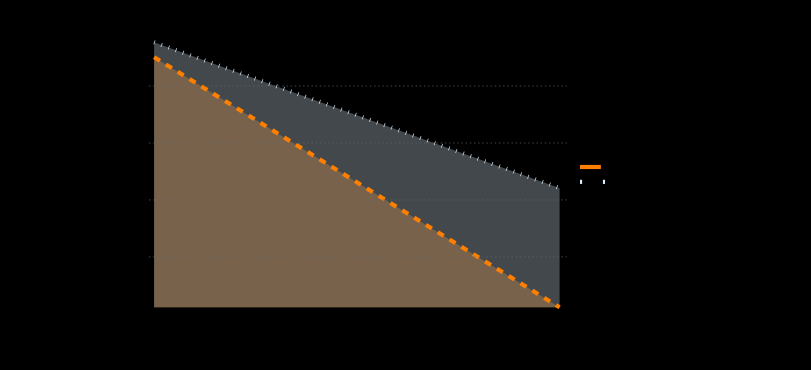

```mathematica
Plot[{modelDaily,modelWeekend},{x,1,5},
PlotLabel->Style["Grade VS Alcohol Consumption (Daily and on Weekend)"],
PlotTheme-> "Business",
Background->Black,
FrameStyle->White,
FrameLabel->{"x","y"},
AxesStyle->None,
PlotStyle->{Directive[Orange, Dashed],Directive[LightBlue, Dotted]},
PlotLegends->Placed[LineLegend["Expressions",LegendFunction->(Framed[#,RoundingRadius->5,Background->Gray]&)],{0.85,0.15}],
ImageSize->{600,400},
Filling->Axis]
```

```mathematica
dataAbsence={absence,numresponse};
dataAbsenceT=Transpose[dataAbsence];
modelAbsence = Normal[LinearModelFit[dataAbsenceT,x,x]]
```

11.81-0.0926266 x

Plotting grade as response to absences from school. The -ve slope evidently implies that grade reduces with increase in number of absences.

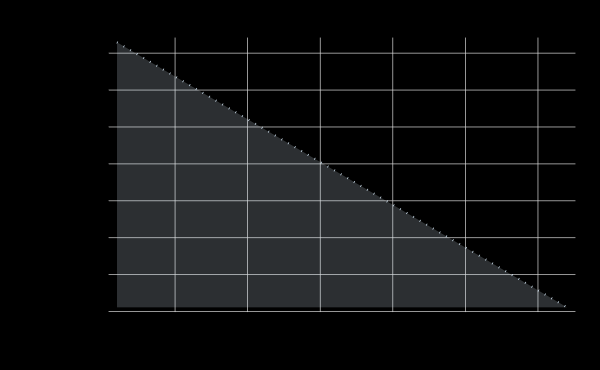

```mathematica
Plot[{modelAbsence},{x,1,32},
PlotLabel->Style["Grade VS Absence"],
PlotTheme-> "Detailed",
Background->Black,
FrameStyle->White,
FrameLabel->{"x","y"},
AxesStyle->None,
PlotStyle->{Directive[LightBlue, Dotted]},
PlotLegends->Placed[LineLegend["Expressions",LegendFunction->(Framed[#,RoundingRadius->5,Background->Gray]&)],{0.85,0.15}],
ImageSize->{600,400},
Filling->Axis]
```

```mathematica
{ListPlot3D[dataDaily, Mesh->2, PlotStyle->Directive[Opacity[0.7],Purple, Specularity[White,50]], ImageSize->Medium],ListPlot3D[dataWeekend, PlotStyle->Directive[Opacity[0.7],Blue, Specularity[White,50]], ImageSize->Medium]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
ListPlot3D[dataAbsence, ImageSize->Medium,ViewPoint-> Front]
```

-Graphics3D-

Below 2 plots shows Variance in data of alcohol consumption daily and on weekend.

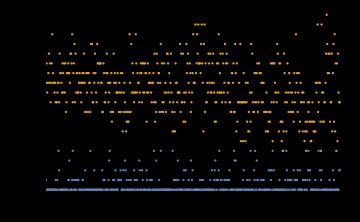

```mathematica
val1=StandardDeviation[dataDaily[[All,1]]]/Sqrt[Length[dataDaily]];
val2=StandardDeviation[dataDaily[[All,2]]]/Sqrt[Length[dataDaily]];
Show[ListPlot[dataDaily],Plot[{modelDaily[x],modelDaily[x+val1],modelDaily[x-val2]},{x,1,5}], ImageSize->Medium, Background->Black]
```

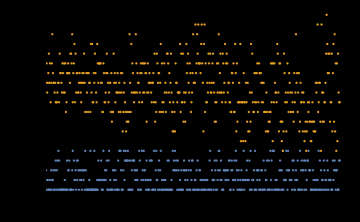

```mathematica
val1=StandardDeviation[dataWeekend[[All,1]]]/Sqrt[Length[dataWeekend]];
val2=StandardDeviation[dataWeekend[[All,2]]]/Sqrt[Length[dataWeekend]];
Show[ListPlot[dataWeekend],Plot[{modelWeekend[x],modelWeekend[x+val1],modelWeekend[x-val2]},{x,1,5}], ImageSize->Medium, Background->Black]
```

## Conclusion

Mathematica offers a great range of options for visualization. It has proven to be a real asset to the modeling of data. However, I have only used a small fraction of the options Mathematica offers. There might be some that would have improved results further. 

With the given sample of data and Linear Regression technique used, model gives R2 around 95% accuracy. Also, the goal of project to study alcohol consumption impact on student’s academic grade was achieved successfully. It has been shown and proved that grade reduces for higher alcohol consumption. 

Even though the Dataset function of Mathematica is relatively new, it offers already a good range of functions for Data Analysis. Especially the visualizations possibilities for the data are very satisfactory.